```mathematica
deu[x1_,x2_]:=x1^2+x2^2
```

```mathematica
dmh[x1_,x2_]:=Abs[x1]+Abs[x2]
```

```mathematica
rquad[d_,c_]:=c/(d+c)
```

```mathematica
gauss[d_]:=Exp[-d]
```

```mathematica
Module[{ran=2},Plot3D[gauss[deu[x,y]],{x,-ran,ran},{y,-ran,ran},PlotRange->All]]
```

-Graphics3D-

```mathematica
Manipulate[Plot[Exp[-gamma*x],{x,0,100},PlotRange->All],{gamma,.001,10}]
```

```mathematica
Manipulate[Plot[{Exp[-gamma1*x],Exp[-gamma2*x^2]},{x,0,8},PlotRange->All],{gamma1,.1,1.},{gamma2,.1,1.}]
```

```mathematica
Manipulate[Plot[{-gamma1*x,-gamma2*x^2},{x,0,8},PlotRange->All],{gamma1,.1,1.},{gamma2,.1,1.}]
```

```mathematica
Module[{ran=4},Plot3D[{gauss[deu[x,y]],rquad[deu[x,y],1]},{x,-ran,ran},{y,-ran,ran},PlotRange->All]]
```

-Graphics3D-

```mathematica
Module[{ran=3,gamma=.01},Plot3D[{gauss[gamma*deu[x,y]],gauss[gamma*dmh[x,y]]},{x,-ran,ran},{y,-ran,ran},PlotRange->All]]
```

-Graphics3D-

```mathematica
Manipulate[Plot3D[{gauss[gamma1*deu[x,y]],gauss[gamma2*dmh[x,y]]},{x,-ran,ran},{y,-ran,ran},PlotRange->All,PlotPoints->50],{ran,.01,10},{gamma1,.01,4.},{gamma2,.01,4.}]
```

```mathematica
Module[{ran=2},Plot3D[{deu[x,y],dmh[x,y]},{x,-ran,ran},{y,-ran,ran},PlotRange->All]]
```

-Graphics3D-

```mathematica
(* rquad kernel *)
```

```mathematica
Manipulate[Plot[{rquad[x,n],sphc[x/12]},{x,0,12},PlotRange->All],{n,.01,30}]
```

```mathematica
Manipulate[Plot3D[{gauss[gamma1*deu[x,y]],rquad[dmh[x,y],gamma2],gauss[gamma3*dmh[x,y]]},{x,-ran,ran},{y,-ran,ran},PlotRange->All,PlotPoints->50],{ran,.01,10},{gamma1,.01,4.},{gamma2,.01,4.},{gamma3,.01,4.}]
```

```mathematica
(* Spherical Kernel *)
```

```mathematica
sphc[d_]:=1-3/2*d+1/2*(d )^3
```

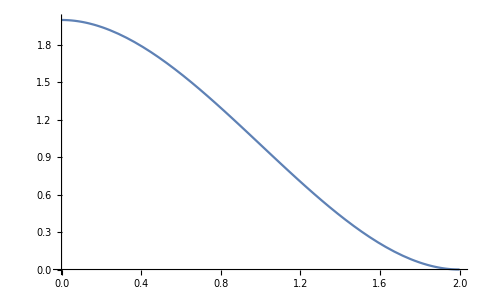

```mathematica
Plot[sphc[x-1],{x,0,2}]
```

```mathematica
D[sphc[x],x]
```

-3/2+(3 x^2)/2

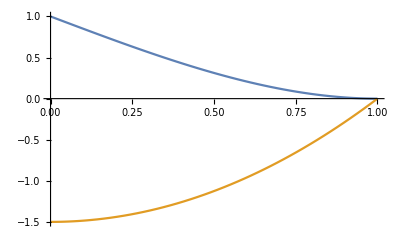

```mathematica
Plot[{sphc[x],-3/2+(3 x^2)/2},{x,0,1}]
```

```mathematica
1-3/2*x/1+1/2*(x/1)^3
```

1-(3 x)/2+x^3/2

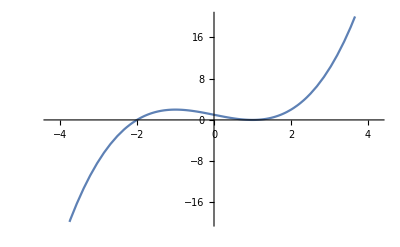

```mathematica
Plot[1-(3 x)/2+x^3/2,{x,-4.242640687119286,4.242640687119286}]
```

```mathematica
(* Circular Kernel *)
```

```mathematica
circ[d_,sigma_]:=2/Pi ArcCos[-d/sigma]-2/Pi*d/sigma*√(1-(d/sigma)^2)
```

```mathematica
Manipulate[Plot[-circ[x,sigma],{x,0,sigma}],{sigma,.1,10}]
```

```mathematica
circ[1,1]
```

2

```mathematica
(* wave kernel *)
```

```mathematica
wave[d_,sigma_]:=sigma/d*Sin[d/sigma]
```

```mathematica
Manipulate[Plot[wave[x,sigma],{x,0,10},PlotRange->All],{sigma,.1,10}]
```

```mathematica
ArcCos[x]
```

ArcCos[x]

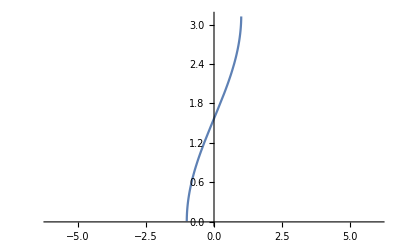

```mathematica
Plot[ArcCos[-x],{x,-6.,6.}]
```

```mathematica
Manipulate[Plot[x^n,{x,0,ran}],{n,.1, 3},{ran,.5, 5}]
```